```mathematica
ClearAll["Global`*"]
```

```mathematica
g[x_]=ArcTan[Exp[ArcTanh[x]]];
h[x_]= g[x]+x/2-ArcTan[x];
H[x_]=h'[x]/g'[x];
dHdr[x_]=H'[x]/g'[x];
Print["H[-1] = ", N[Limit[H[x],x->-1,Direction->"FromAbove"]]]
Print["H[1] = ", N[Limit[H[x],x->1,Direction->"FromBelow"]]]
Plot[{g[x],Pi/2,H[x],dHdr[x]},{x,-1,1},PlotLabels->{"r_*", None, "H","dHdr"},PlotLabel->"H=dh/dr_*, |H|<=1, H[+/-1]=+/-1, dH/dr_*[+/-1]=0"]
```

H[-1] = 1.

H[1] = 1.

-Graphics-

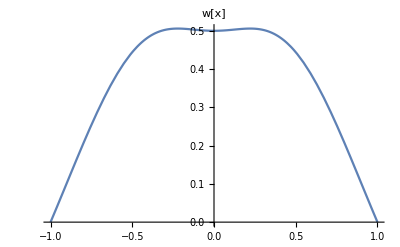

w[-1] = 0. w[1] = 0.

-1/2*((-1 + x^2)*(2 - Sqrt[1 - x^2] + x^2*(2 + Sqrt[1 - x^2])))/(1 + x^2)^2

```mathematica
w[x_]=(g'[x]g'[x]-h'[x]h'[x])/g'[x]//TrigToExp//FullSimplify;
Plot[w[x],{x,-1,1},PlotLabel->"w[x]"]
Print["w[-1] = ", N[Limit[w[x],x->-1,Direction->"FromAbove"]], " w[1] = ", N[Limit[w[x],x->1,Direction->"FromBelow"]]]
InputForm[w[x]]
```

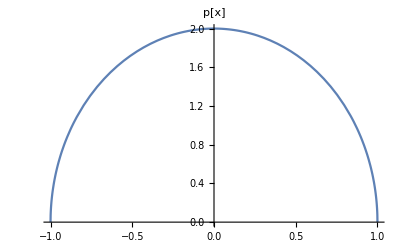

2*Sqrt[1 - x^2]

```mathematica
p[x_]=1/g'[x]//TrigToExp//FullSimplify;
InputForm[p[x]]
Plot[p[x],{x,-1,1},PlotLabel->"p[x]"]
```

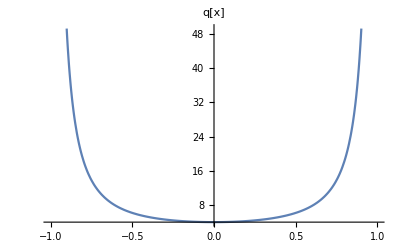

(-(l*(1 + l)*(-1 + x)) + 2*(1 + x))/(1 - x^2)^(3/2)

```mathematica
q[x_]=g'[x](Tan[g[x]]^2+1)(2+l(l+1)/Tan[g[x]]^2)//TrigToExp//FullSimplify;
InputForm[q[x]]
Plot[q[x]/.l->1,{x,-1,1},PlotLabel->"q[x]"]
```

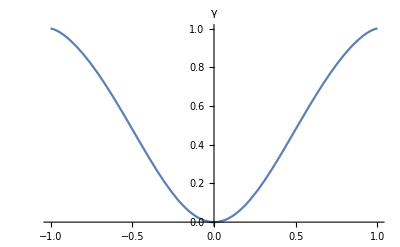

1 + Sqrt[1 - x^2] - (2*Sqrt[1 - x^2])/(1 + x^2)

```mathematica
gamma[x_]=h'[x]/g'[x]//TrigToExp//FullSimplify;
Plot[gamma[x],{x,-1,1},PlotLabel->"γ"]
InputForm[gamma[x]]
```

{0.00199953,-0.00340719,-0.0123671,-0.0155628,0.0186632,-0.0225827,0.0258578,0.0379329,0.039737,-0.0417134,-0.0503807,-0.0538737,0.0599425,-0.062992,0.0675619,0.0762983,0.0829741,-0.0837885,-0.0880583,-0.0979026,0.0994048,-0.105191,0.111953,0.117799,0.120102,-0.123134,-0.130583,0.13998,-0.140665,-0.146242,0.153752,0.158647,0.160877,-0.16685,-0.169797,0.179558,-0.180932,-0.188604,0.19341,0.198041,0.205489,-0.208705,-0.215861,-0.217667,0.218893,0.230264,-0.231372,0.236016,0.238821,0.248551,-0.24989,-0.250772,-0.258026,0.259204,-0.26392,-0.273067,0.276308,0.278394,0.286286,-0.294541,-0.29626,0.296977,-0.30661,0.316098,-0.316676,0.322177,0.3252,-0.332608,0.336015,-0.340198,-0.347574,0.354317,-0.359345,0.361272,0.369211,0.37556,-0.378395,-0.380575,-0.387736,0.392703,0.400428,-0.402857,0.411852,0.412929,-0.421612,-0.424502,-0.426536,0.431287,0.443342,-0.447141,0.448012,0.454556,-0.458795,-0.467895,0.468263,-0.470376,0.481587,0.486537,-0.489037,-0.490971}

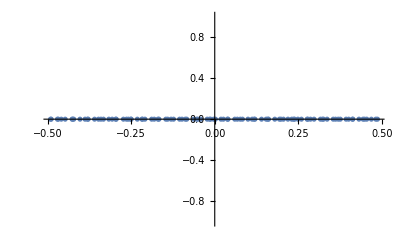

```mathematica
vals = NDEigenvalues[w[x]D[u[t,x],{t,2}]-(p'[x]D[u[t,x],x]+p[x]D[u[t,x],{x,2}]-q[x]u[t,x])-(2gamma[x]D[u[t,x],x,t] +D[gamma[x],x]D[u[t,x],t])/.l->0,u[t,x],{t,N[h[-1]],500},{x,-0.999999,0.999999}, 100,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi","MaxIterations"->10000,"BasisSize"->500}}]
ListPlot[Table[{Re[ vals[[i]]],Im[vals[[i]]]},{i,1,Length[vals]}],PlotRange->Full]
```

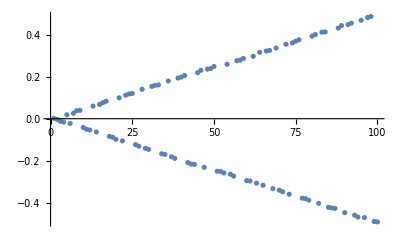

```mathematica
ListPlot[vals]
```

```mathematica
InputForm[p[x]/w[x]//TrigToExp//FullSimplify]
```

(-1/4 - (1 + x^2)^(-2) + (1 + x^2)^(-1) + Sqrt[1 - x^2]/(2 + 2*x^2))^(-1)

```mathematica
InputForm[p'[x]/w[x]//TrigToExp//FullSimplify]
```

(4*x*(1 + x^2)^2)/(1 - 3*x^2 - x^6 - 2*Sqrt[1 - x^2] + x^4*(3 + 2*Sqrt[1 - x^2]))

```mathematica
InputForm[q[x]/w[x]//TrigToExp//FullSimplify]
```

(2*(1 + x^2)^2*(l*(1 + l)*(-1 + x) - 2*(1 + x)))/((-1 + x^2)^2*(1 + x^4 - 2*Sqrt[1 - x^2] - 2*x^2*(1 + Sqrt[1 - x^2])))

```mathematica
InputForm[gamma[x]/w[x]//TrigToExp//FullSimplify]
```

(-2*(1 + x^2)*(1 - Sqrt[1 - x^2] + x^2*(1 + Sqrt[1 - x^2])))/((-1 + x^2)*(2 - Sqrt[1 - x^2] + x^2*(2 + Sqrt[1 - x^2])))

```mathematica
InputForm[D[gamma[x],x]/w[x]//TrigToExp//FullSimplify]
```

(-2*x*(5 + x^2))/(1 + x^4 - 2*Sqrt[1 - x^2] - 2*x^2*(1 + Sqrt[1 - x^2]))

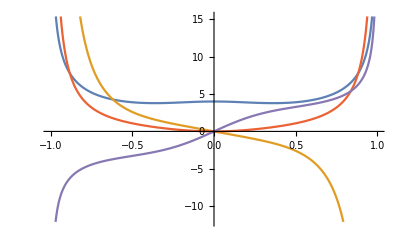

```mathematica
Plot[{p[x]/w[x],p'[x]/w[x],q[x]/w[x],gamma[x]/w[x],gamma'[x]/w[x]},{x,-1,1}]
```